```mathematica
DD[ k_, a_, n_ ] := Sum[ Binomial[k,j] DD[ k-j, m+1, Floor[n/(m^j)]], {m,a, n^(1/k)},{j,1,k}]
DD[ 1,a_, n_ ]:= Floor[n]-a+1
DD[0,a_,n_] := 1
DS[ n_, k_ ] := DD[k,2,n]
DDD[n_, k_ ] := Sum[ DDD[n/j, k-1],{j,2,n}]
DDD[n_,0] := 1
D2[1,a_,n_,p_,r_] := n-a+1
D2[2,a_,n_,p_,r_] := p/((r+1)(r+2)) + (Floor[n/a]-a)(p/(r+1))+(Floor[n^(1/2)]-a)(p/2) + p Sum[ Floor[n/m] - m,{m,a+1, n^(1/2)}]
D2[k_, a_,n_,p_,r_] := D2[k-1, a, n/a, p/(r+1), r+1] + Sum[ D2[ k-1, m, n/m, p, 1 ], {m,a+1, n^(1/k)}]
DD2[ n_, k_] := D2[ k, 2, n, k!, 0 ]
D3[1,a_,n_,p_,r_] := p/(r+1) + p (Floor[n]-a)
D3[k_, a_,n_,p_,r_] := D3[k-1, a, n/a, p/(r+1), r+1] + Sum[ D3[ k-1, m, n/m, p, 1 ], {m,a+1, n^(1/k)}]
DD3[ n_, k_] := D3[ k, 2, n, k!, 0 ]
D4[1,a_,n_,p_,r_] :=  p (Floor[n]-a+1)-p/(r+1) 
D4[k_, a_,n_,p_,r_] := Sum[ D4[ k-1, m, n/m, p, 1 ], {m,a, n^(1/k)}]-D4[k-1, a, n/a, p/(r+1), r+1]
DD4[ n_, k_] := D4[ k, 1, n, k!, 0 ]
```

```mathematica
DDD[1000,4]
```

13952

```mathematica
DD4[1000,4]
```

13952

```mathematica
D5[1,a_,n_,p_,r_,s_] := s!/p/(r+1) + (s!/p) (Floor[n]-a)
D5[k_, a_,n_,p_,r_, s_] := D5[k-1, a, n/a, p(r+1), r+1,s+1] + Sum[ D5[ k-1, m, n/m, p, 1,s+1], {m,a+1, n^(1/k)}]
DD5[ n_, k_] := D5[ k, 2, n, 1, 0,1]
```

```mathematica
DD5[1000,3]
```

11217

```mathematica
DDD[1000,3]
```

11217

```mathematica
D6[1,a_,n_,p_,r_,s_] := p + (p(r+1)) (Floor[n]-a)
D6[k_, a_,n_,p_,r_, s_] := D6[k-1, a, n/a, p, 1,s+1] + Sum[ D6[ k-1, m, n/m, p (r+1), r+1,s+1], {m,a+1, n^(1/k)}]
DD6[ n_, k_] := D6[ k, 2, n, 1, 0,1]
```

```mathematica
DD6[1000,3]
```

10655

```mathematica
DA[ 1, n_, a_, k_, p_, r_ ]:= (p/r +  p (Floor[n]-a))
DA[s_, n_,a_, k_,p_,r_] := DA[s-1, n/a, a,k+1, k p/ r, r+1]+ Sum[ DA[s-1, n/m, m,k+1, k p, 2], {m,a+1, n^(1/s)}]
DDA[ n_, s_] := DA[ s,n, 2, 2, 1, 1]
```

```mathematica
DDD[1000,3]
```

11217

```mathematica
DDA[1000,3]
```

11217

```mathematica
DB[ 1, n_, a_, k_, p_, r_ ]:=  p (Floor[n]-a+1) - p/r
DB[s_, n_,a_, k_,p_,r_] := Sum[ DB[s-1, n/m, m,k+1, k p, 2], {m,a, n^(1/s)}]-DB[s-1, n/a, a,k+1, k p/ r, r+1]
DDB[ n_, s_] := DB[ s,n, 1, 2, 1, 1]

DDD[1000,3]
```

11217

```mathematica
DDB[1000,3]
```

11217

```mathematica
D7[a_,n_,p_,r_, s_] := 
(s!/p/r + (s!/p) (Floor[n]-a))/s-
If[ n^(1/2)≥ a ,D7[a, n/a, p r, r+1,s+1] + 
Sum[ D7[m, n/m, p, 2,s+1], {m,a+1, n^(1/2)}], 0]
DD7[ n_] := D7[ 2, n, 1, 1,1]
```

```mathematica
DD7[100]
```

428/15

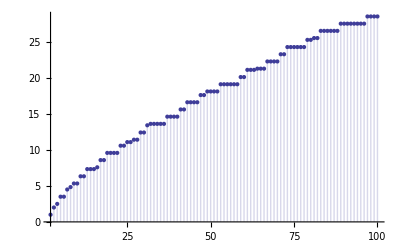

```mathematica
DiscretePlot[ DD7[n],{n,2,100}]
```

```mathematica
D8[s_Number,n_Number,a_Integer, k_Integer,p_Integer,r_Integer] := 
p( Floor[n/s]*s-a + 1/r)-
If[ n^(1/2)≥ a , Sum[ D8[s, n/m, m,k+1, k p/ r, r+1]*s, {m, a, a+.999999, s}], 0] - 
 Sum[ D8[s,n/m, m,k+1, k p, 2]*s, {m,a+1, n^(1/2), s}]
DD8[ n_, s_] := D8[ s,n, 1+s, 1, 1, 1]

D8a[n_,a_, k_,p_,r_] := 
p( Floor[n]-a + 1/r)-
If[ n^(1/2)≥ a , D8a[n/a, a,k+1, k p/ r, r+1], 0] - 
 Sum[ D8a[n/m, m,k+1, k p, 2], {m,a+1, n^(1/2)}]
DD8a[ n_] := D8a[ n, 2, 1, 1, 1]
```

```mathematica
DD8[100,.1]
```

29.3156

```mathematica
DD8[100,.2]
```

28.9508

```mathematica
DD8[100,.3]
```

30.848

```mathematica
DD8[100,.5]
```

29.2466

```mathematica
N[DD8[100,1]]
```

28.5333

```mathematica
DD8[100,.05]
```

$Aborted

```mathematica
DD8a[ 100]
```

428/15

```mathematica
DD9[n_, k_,a_] := Sum[ (-1)^(j-1) Binomial[k,j] DD9[ n/(m^j), k-j, m], {j,1,k},{m,a,n^(1/k)}]
DD9[n_, 0,a_]:=1
DD9[1000, 5,2]
10602
DDD[1000,5]
10602
DiscretePlot[DD9[n,4,2],{n,2,1000}]
```